# GRADOS EN INGENIERÍA TELEMÁTICA E INGENIERÍA DE TECNOLOGÍAS DE TELECOMUNICACIÓN Métodos Matemáticos de las Telecomunicaciones (curso 23 - 24) Practica 0 (3 de 4). Curvas en paramétricas e implícitas.

## Ejercicio 1

Dibujar la curva γ≡{x=(t (t^2-1))/(1+t^2)
y=(2 (t^2-1))/(1+t^2)  t ϵ [-5,4] e indicar su sentido de recorrido.

```mathematica
γ[t_] = {(t * (t^2 - 1))/(1 +t^2), (2 * (t^2 - 1))/(1 + t^2)}
```

{(t (-1+t^2))/(1+t^2),(2 (-1+t^2))/(1+t^2)}

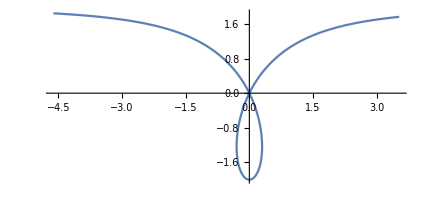

```mathematica
ParametricPlot[γ[t], {t, -5, 4}]
```

```mathematica
puntoInicial = N[ γ[-5]]
```

{-4.61538,1.84615}

```mathematica
puntoFinal = N[γ[4]]
```

{3.52941,1.76471}

## Ejercicio 2

Dibujar la misma curva del ejercicio anterior pero recorrida en sentido contrario.

```mathematica
β[t_] = γ[-t];
```

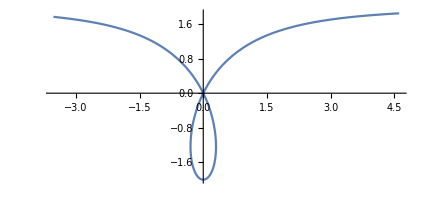

```mathematica
ParametricPlot[β[t] , {t, -5, 4}]
```

```mathematica
puntoI = N[β[-4] ]
```

{3.52941,1.76471}

```mathematica
PuntoFi = N[β[5] ]
```

{-4.61538,1.84615}

## Ejercicio 3

Dibujar la hélice γ≡{x=2cos t
y =2sen t 
z=0.1 t  con t∈[0,10 π].

```mathematica
ParametricPlot3D[{2* Cos[t], 2 * Sin[t], 0.1t}, {t, 0 , 10Pi}, AxesLabel -> {"Eje X", "Eje Y", "Eje Z"}]
```

-Graphics3D-

## Ejercicio 4

Parametrizar las siguientes figuras:
a) -Graphics-  b) -Graphics-

```mathematica
γ[t_] = {3Cos[t], 3Sin[t]}
```

{3 Cos[t],3 Sin[t]}

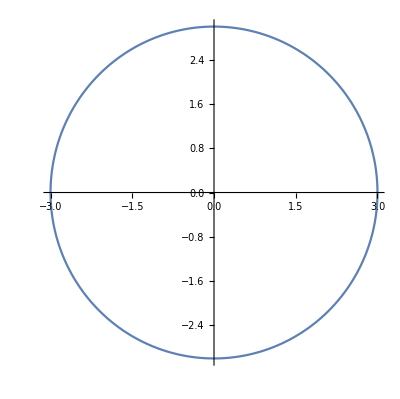

```mathematica
ParametricPlot[γ[t], { t, 0, 2Pi}, AxesOrigin->{0,0}]
```

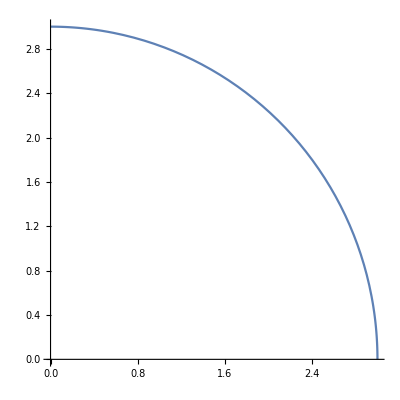

```mathematica
ParametricPlot[γ[t], { t, 0, Pi/2}, AxesOrigin->{0,0}]
```

## Ejercicio 5

Parametrizar la circunferencia centrada en el punto (3,4) de radio 2

(x - 3)^2 + (y - 4)^2 = 2^2
x - 3 = 2cosϑ; x = 2cosϑ + 3
y - 4 = 2senϑ; y = 2senϑ + 4

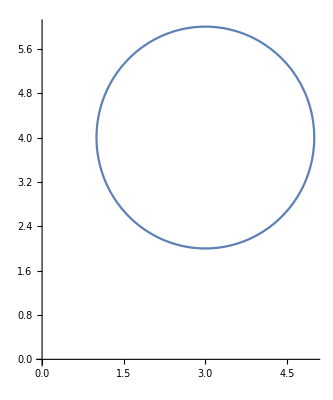

```mathematica
γ[t_] = {2Cos[t] + 3, 2Sin[t] + 4};
ParametricPlot[γ[t], {t,0,2Pi}, AxesOrigin->{0,0}]
```

## Ejercicio 6

Parametrizar las siguientes figuras:
a) La elipse x^2/3^2+y^2/2^2=1
b)

```mathematica
γ[t_] = {3Cos[t], 2Sin[t]};
```

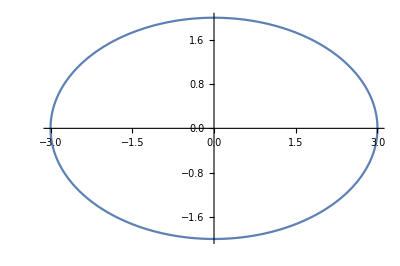

```mathematica
ParametricPlot[γ[t], {t,0,2Pi}, AxesOrigin->{0,0}]
```

```mathematica
puntoInicial = {1, 2, -1};
puntoFinal = {2, 0, -1};
vector = puntoFinal - puntoInicial
```

{1,-2,0}

```mathematica
γ[t_] = puntoInicial + t * vector
```

{1+t,2-2 t,-1}

```mathematica
ParametricPlot3D[γ[t], {t,0, 1}, AxesLabel -> {"Eje X", "Eje Y", "Eje Z"}]
```

-Graphics3D-

$Failed

## Ejercicio 7

a) Dibujar el punto (3,4) en color verde.
b) Dibujar el vector que parte del punto (1,1) y termina en el punto (3,2).
c) Dibujar el vector que parte del punto (0,1,1) y termina en el punto (-1,0,1).

## Ejercicio 8

a) Sea la curva en paramétricas γ(t)≡{x=sen t
y =t^2 
z=sen t cos t  con t∈[0,2] y calcular su vector tangente en el punto (1/(√2),π^2/16,1/2).

b) Dibujar la curva junto con el punto (1/(√2),π^2/16,1/2) y el vector tangente obtenido en el apartado a).

La longitud L de una curva parametrizada en ℝ^2 o  ℝ^3 viene dada por la expresión: 
																		L=∫_a^b |γ'(t) |dt

## Ejercicio 9

Calcular la longitud de la curva anterior: γ(t)≡{x=sen t
y =t^2 
z=sen t cos t  con t∈[0,2].

Mathematica tiene la posibilidad de dibujar funciones dadas de forma implícita F(x,y)=0 con la orden ContourPlot.

## Ejercicio 10

Dibujar la elipse x^2/3^2+y^2/2^2=1.